```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Clear[τ]
```

```mathematica
ABcounts={380,387,400,390,391,346,403,381,383,339,420,407,397,372,399,398}
```

{380,387,400,390,391,346,403,381,383,339,420,407,397,372,399,398}

```mathematica
ABcounts/20
```

{19,387/20,20,39/2,391/20,173/10,403/20,381/20,383/20,339/20,21,407/20,397/20,93/5,399/20,199/10}

```mathematica
Mean[%]
```

6193/320

```mathematica
N[6193/320]
```

19.3531

```mathematica
Length[ABcounts]
```

16

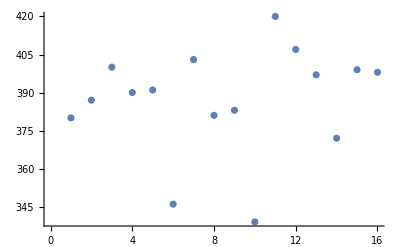

```mathematica
ListPlot[ABcounts]
```

```mathematica
ABcps=Mean[ABcounts]/20//N
```

19.3531

```mathematica
StandardDeviation[ABcounts]//N
```

20.9999

```mathematica
StandardDeviation
```

StandardDeviation

```mathematica
Sqrt[387.063]/20
```

0.983696

```mathematica
ABTrate={{1000,3/380},{1050,6/387},{1100,2/400},{1150,1/390},{1200,6/334},{1250,7/391},{1300,23/346},{1350,47/403},{1400,75/381},{1450,253/1092},{1500,327/1254}}
```

{{1000,3/380},{1050,2/129},{1100,1/200},{1150,1/390},{1200,3/167},{1250,7/391},{1300,23/346},{1350,47/403},{1400,25/127},{1450,253/1092},{1500,109/418}}

```mathematica
r={3,6,2,1,6,7,23,47,75,253,327};
```

```mathematica
n={380,387,400,390,334,391,346,403,381,1092,1254};
```

```mathematica
p=Table[r⟦i⟧/n⟦i⟧,{i,1,Length[r]}];
```

```mathematica
ABTrate=Table[{1000+50 (i-1),p⟦i⟧},{i,1,Length[p]}];
```

```mathematica
ABTrateError=Table[ErrorBar[25,Sqrt[p⟦i⟧(1-p⟦i⟧)/n⟦i⟧]],{i,1,Length[p]}];
```

```mathematica
ABTerrorList=Table[{ABTrate⟦i⟧,ABTrateError⟦i⟧},{i,1,Length[r]}];
```

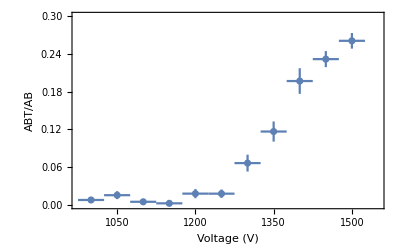

```mathematica
ErrorListPlot[ABTerrorList,PlotRange->{{975,1550},{0,0.30}},Frame->True,FrameLabel->{"Voltage (V)","ABT/AB"}]
```

```mathematica
ABTVrate={{1350,48/383},{1365,45/339},{1380,51/420},{1395,43/407},{1410,48/397},{1425,49/372},{1440,55/399},{1455,38/398},{1470,43/498},{1485,109/1111},{1500,111/1177}}
```

{{1350,48/383},{1365,15/113},{1380,17/140},{1395,43/407},{1410,48/397},{1425,49/372},{1440,55/399},{1455,19/199},{1470,43/498},{1485,109/1111},{1500,111/1177}}

```mathematica
r2={48,45,51,43,48,49,55,38,43,109,111};
```

```mathematica
n2={383,339,420,407,397,372,399,398,498,1111,1177};
```

```mathematica
p2=Table[r2⟦i⟧/n2⟦i⟧,{i,1,Length[r2]}];
```

```mathematica
ABTVrate=Table[{1350+15 (i-1),p2⟦i⟧},{i,1,Length[p2]}];
```

```mathematica
ABTVrateError=Table[ErrorBar[5,Sqrt[p2⟦i⟧(1-p2⟦i⟧)/n2⟦i⟧]],{i,1,Length[p2]}];
```

```mathematica
ABTVerrorList=Table[{ABTVrate⟦i⟧,ABTVrateError⟦i⟧},{i,1,Length[r2]}];
```

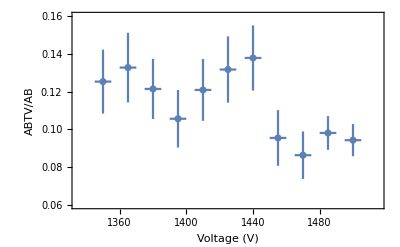

```mathematica
ErrorListPlot[ABTVerrorList,PlotRange->{{1335,1515},{0.06,0.16}},Frame->True,FrameLabel->{"Voltage (V)","ABTV/AB"}]
```

```mathematica
path="/Users/jackson/Muon-Lifetime/data/"
```

/Users/jackson/Muon-Lifetime/data/

```mathematica
data1=Import[StringJoin[path,"data1.csv"],"Data"];
```

```mathematica
time1=data1[[14]][[2]]
```

172889.

```mathematica
data1=data1⟦23;;⟧;
```

```mathematica
data2=Import[StringJoin[path,"data2.csv"],"Data"];
```

```mathematica
time2=data2[[14]][[2]]
```

532414.

```mathematica
data2=data2⟦23;;⟧;
```

```mathematica
data3=Import[StringJoin[path,"data3.csv"],"Data"];
```

```mathematica
time3=data3[[14]][[2]]
```

89071.5

```mathematica
data3=data3⟦23;;⟧;
```

```mathematica
data4=Import[StringJoin[path,"data4.csv"],"Data"];
```

```mathematica
time4=data4[[14]][[2]]
```

171998.

```mathematica
data4=data4⟦23;;⟧;
```

```mathematica
data5=Import[StringJoin[path,"data5.csv"],"Data"];
```

```mathematica
time5=data5[[14]][[2]]
```

91663.6

```mathematica
data5=data5⟦23;;⟧;
```

```mathematica
dataTotal=Table[{data1⟦i⟧⟦1⟧*(8/1000),data1⟦i⟧⟦3⟧+data2⟦i⟧⟦3⟧+data3⟦i⟧⟦3⟧+data4⟦i⟧⟦3⟧+data5⟦i⟧⟦3⟧},{i,1,Length[data1]}];
```

```mathematica
dataTotal=dataTotal⟦11;;⟧;
```

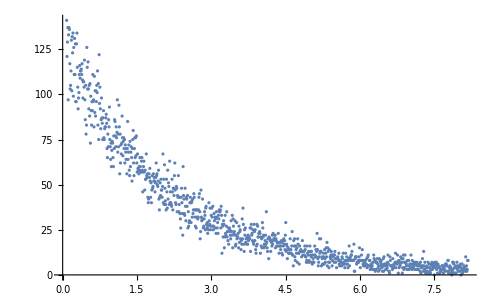

```mathematica
ListPlot[dataTotal]
```

```mathematica
Clear[τ]
```

```mathematica
fit=NonlinearModelFit[dataTotal,N0 E^(-t/τ),{N0,τ},t]
```

FittedModel[128.547 ⅇ^(-0.481831 t)]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
N0 | 128.547 | 0.83003 | 154.87 | 5.02041953979×10^-707
τ | 2.07542 | 0.0184057 | 112.759 | 2.68465856008×10^-575

```mathematica
tempData=Cases[dataTotal,{x_,y_}/;y≠0];
```

```mathematica
logData=Table[{tempData⟦i⟧⟦1⟧,Log[tempData⟦i⟧⟦2⟧]//N},{i,1,Length[tempData]}];
```

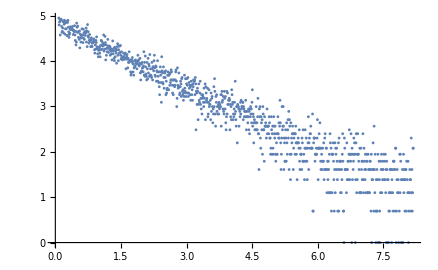

```mathematica
ListPlot[logData]
```

```mathematica
Clear[x]
```

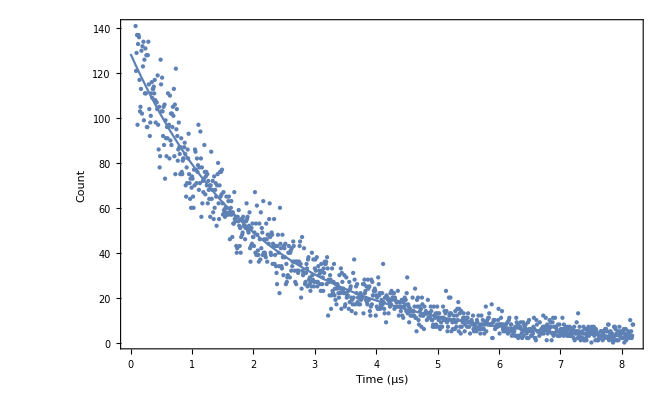

```mathematica
Show[ListPlot[dataTotal],Plot[fit[z],{z,0,8}],Frame->True,FrameLabel->{"Time (μs)","Count"}]
```

```mathematica
linearFit=LinearModelFit[logData,x,x,Weights->(Sqrt[#2]&)]
```

FittedModel[4.77681-0.451019 x]

```mathematica
linearFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.77681 | 0.01683 | 283.827 | 2.25937803216×10^-951
x | -0.451019 | 0.00394579 | -114.304 | 5.04503668691×10^-573

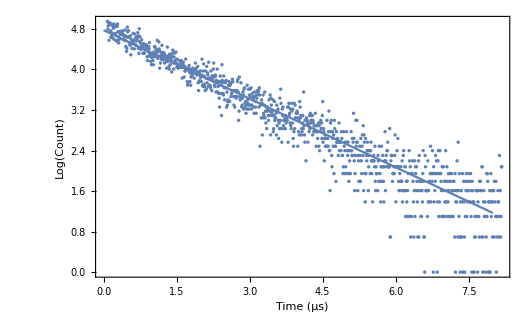

```mathematica
Show[ListPlot[logData],Plot[linearFit[x],{x,0,8}],Frame->True,FrameLabel->{"Time (μs)","Log(Count)"}]
```

```mathematica
τ=1/0.4510188306427054
```

2.2172

```mathematica
στ=0.01840569774438395
```

0.0184057

```mathematica
(τ-2.197)/2.197*100
```

1.65509

#### Linear Fit

```mathematica
linearλp=0.4510188306427054+0.003945787586049315
```

0.454965

```mathematica
linearλm=0.4510188306427054-0.003945787586049315
```

0.447073

```mathematica
linearτp=1/linearλp
```

2.19797

```mathematica
linearτm=1/linearλm
```

2.23677

```mathematica
avglinearτ=(linearτp+linearτm)/2
```

2.21737

```mathematica
σlinearτ=linearτm-avglinearτ
```

0.0193989

```mathematica
(τ-2.197)/σlinearτ
```

1.04141

### Subtracting Background

```mathematica
timeDataTotal=Table[{dataTotal⟦i⟧⟦1⟧*10^(-6),dataTotal⟦i⟧⟦2⟧},{i,1,Length[dataTotal]}]//N;
```

```mathematica
numABEventsPerDeltaT=Table[ABcps*timeDataTotal⟦i⟧⟦1⟧,{i,1,Length[timeDataTotal]}];
```

```mathematica
testData=Table[{dataTotal⟦i⟧⟦1⟧,dataTotal⟦i⟧⟦2⟧-numABEventsPerDeltaT⟦i⟧},{i,1,Length[dataTotal]}]//N;
```

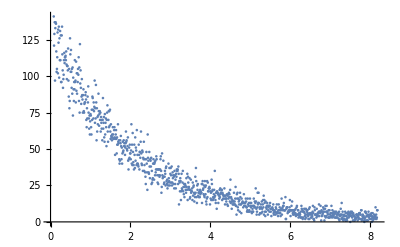

```mathematica
ListPlot[testData]
```

```mathematica
Clear[τ]
```

```mathematica
fit=NonlinearModelFit[testData,N0 E^(-t/τ),{N0,τ},t]
```

FittedModel[128.547 ⅇ^(-0.481833 t)]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
N0 | 128.547 | 0.83003 | 154.87 | 5.0191682896×10^-707
τ | 2.07541 | 0.0184056 | 112.759 | 2.6834172681×10^-575